Borrowing from the work in Notermans’ thesis, let’s consider the transitions we’re driving. Denote the metastable state population ρ_11, the excited state ρ_22, and the cooling state ρ_33. There is also a loss channel from the excited state to other states in the 2p manifold - denote these collectively by ρ_44. Assume that the other 2p states don’t decay back to the trapped metastable state, and the upper cooling state always decays to the metastable state*, We have the rates
A_21= 6.4 e^-9 Hz
A_32= 1.5 e^7 Hz
A_31= 1.02 e^7 Hz
With an additional loss channel from the excited 3^3 S_1state to the m=0,1 states of the 2^3 P_2 state with rate A_24 = 1.2 e^7Hz
and from the metastable state to the true ground state with rate
A_14=  1.272 e^-4 Hz

The populations evolving under the optical Bloch equations read:
(ρ̇)_11 =A_21 ρ_22+ A_31 ρ_33+ⅈ Ω/2(ρ_21-ρ_12) 
(ρ̇)_22 =-(A_23+A_21 + A_42)ρ_22-ⅈ Ω/2(ρ_21-ρ_12) 
(ρ̇)_33 =A_23 ρ_22- A_13 ρ_33
(ρ̇)_44= A_24 ρ_22
With coherences
(ρ̇)_12 =-((Γ_1+Γ_2)/2+ⅈΔ)ρ_12+ⅈΩ/2(ρ_22-ρ_11)
(ρ̇)_13=- Γ_1/2 ρ_13
(ρ̇)_23 = -Γ_2/2 ρ_23 
(ρ̇)_24 = -Γ'_2/2 ρ_44 
Where Ω^2 = (3 πc^2)/ℏω_0^2 A_21 I_0=  (3 πc^2)/ℏω_0^2 A_21(2P)/(π w_0^2)

Let us approximate these rates by the respective linewidths, noting A_21 is absolutely tiny, and approximating (for simplicity for now) L=A_23+ A_24, and q=ⅈ(ρ_21-ρ_12)/2
(ρ̇)_11 = Γ_3 ρ_33+ⅈΩ(ρ_21-ρ_12)/2 
(ρ̇)_22 =-L ρ_22-ⅈΩ(ρ_21-ρ_12)/2 
(ρ̇)_33 =L/2 ρ_22- Γ_3 ρ_33
(ρ̇)_44= A_24 ρ_22≃L/2 ρ_22
With coherences
(ρ̇)_12 =-(Γ_2/2+ⅈΔ)ρ_12+ⅈΩ/2(ρ_22-ρ_11)
(ρ̇)_13=- Γ_3/2 ρ_13
(ρ̇)_23 = -Γ_2/2 ρ_23 
(ρ̇)_24 = -Γ'_2/2 ρ_44
Our next task is to solve this system of coupled linear differential equations.
Probably need to add in by losses from the metastable state, as they’re faster than the one we’re trying to drive!!!

```mathematica
BlochEqns[Ω_,Γ1_,Γ2_,Γ3_,Δ_]:= {ρ11'[t] == Γ3 *ρ33[t]+ⅈ Ω (ρ21[t]-ρ12[t])/2-Γ1*ρ11[t],
ρ22'[t] == -Γ2 *ρ22[t]-ⅈ Ω (ρ21[t]-ρ12[t])/2,
ρ33'[t] == Γ2/2*ρ22[t]-Γ3*ρ33[t],
ρ12'[t]==-((Γ1+Γ2)/2+ⅈ Δ)ρ12[t]+(ⅈ Ω)/2(ρ22[t] - ρ11[t]),
ρ21'[t]==-((Γ1+Γ2)/2-ⅈ Δ)ρ21[t]-(ⅈ Ω)/2(ρ22[t] - ρ11[t])};
initCond= {ρ11[0] ==1, ρ22[0] == 0, ρ33[0] == 0, ρ21[0 ] == 0, ρ12[0] == 0};
```

```mathematica
delsolve[Ω_,Δ_] := NDSolve[Flatten[{BlochEqns[Ω,1.27*10^-4,2.7*10^7,1.02*10^7,Δ],initCond}],{ρ11,ρ22,ρ33,ρ12,ρ21},{t,0,10}];
```

```mathematica
P = 60*10^-3;
w = 20*10^-6;
ω0 = 2*π*7.02*10^14;
c = 299792458;
A21 = 6.4*10^-9;
ℏ = (6.63*10^-34)/(2π);
RabiFreq = √((3π c^2)/(ℏ ω0^3)A21*(2P)/(π w^2));
detunings = Table[i*10^6,{i,-50,50,2}];
dsolns = Map[delsolve[RabiFreq,#1]&,detunings];
```

```mathematica
1-ρ11[1]/.delsolve[RabiFreq,0]
```

{0.001185+0. ⅈ}

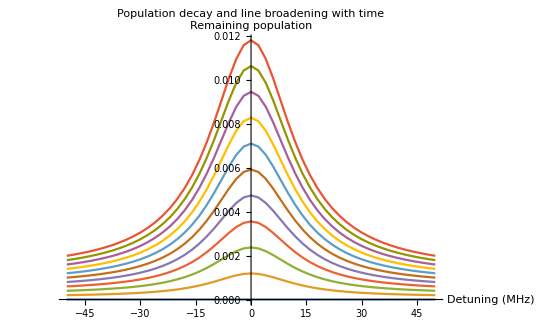

```mathematica
linedata = Table[Transpose[{detunings*10^-6,1-Flatten[ρ11[t]/.dsolns]}],{t,0,10}];
ListLinePlot[linedata,PlotLabel->"Population decay and line broadening with time",AxesLabel->{"Detuning (MHz)","Remaining population"},PlotRange->Full]
```

```mathematica
wbar = 2*π*(450*450*50)^(1/3);
mHe = 6.64*10^-27;
q = 1.6*10^-19;
Eho = ℏ wbar;
eV = Eho/q
kB = 1.308*10^-23;
```

8.96448×10^-13

```mathematica
(2*3000*q)/m
```

380235.

```mathematica
λ = 427*10^-9;
k = (2π)/λ;
(ℏ k)/mHe
```

0.233839

1.40352

```mathematica
dT=0.001(ℏ k)^2/(2 mHe kB)
```

1.38792×10^-8

```mathematica
;Tc = (0.94*ℏ*wbar*Natom^(1/3))/kB
```

1.03078×10^-6

```mathematica
((1.38*10^-8)/(1.03*10^-6))^3
```

2.40506×10^-6

```mathematica
4.5*wbar/100*Natom^(1/3)
```

6116.8

So we don’t scatter many photons; maybe 0.1% of the atoms are excited. A single photon recoil gives an atom velocity

```mathematica
vRecoil = (ℏ k)/mHe
```

0.233839

Which is smaller than the mean MOT velocity and hence remains trapped

```mathematica
vMOT=√((8kB*10^-3)/(π mHe))(*Mean of maxwellian distribution at mK*)
```

2.2397

Assuming this energetic atom subsequently thermalizes with the cloud, this distributes the kinetic energy evenly among the 6N degrees of freedom. 
The average kinetic energy per particle is then 1/(6N)m_He v_recoil^2. Assuming this distributes evenly through all dof,

```mathematica
Natom=10^6;
meanenergy=(mHe*vRecoil^2)/(6*Natom);
TempPerPhoton = meanenergy/kB;
totalHeat = 0.001*Natom*TempPerPhoton
```

4.62641×10^-9

```mathematica
ℏ/(mHe 10^-6)
```

0.0158915

```mathematica
aS = 7.5*10^-9;
n = 10^19;
n*√2*aS*√((8kB*10^-6)/(π mHe))
```

7.51218×10^9

The recoil velocity from a single photon would produce a displacement at the detector; atoms immediately untrapped will have this velocity away from the trap centre, putting them just off the edge of the detector

```mathematica
0.23*0.417
```

0.09591

Considering whether outcoupling excited atoms could let them fall on the detector. Atoms initially have velocity vRecoil and kinetic energy 1/2 mHe*vRecoil^2. The lifetime of the excited state is some 10s of ns;

```mathematica
τ = 1/(2.7*10^7)
```

3.7037×10^-8

Which is much faster than the trap dynamics. The atoms will therefore have some velocity kick up to 2*vRecoil. This determines how far they make it up the magnetic field. From conservation of energy:
max(KE) = max(PE)
1/2 m vRecoil^2 = g μB |B|
⇒|B| =

```mathematica
μB = 9.27*10^-29;
Bmax = (mHe * vRecoil^2)/(4*μB)
```

0.979182

This specifies the Zeeman splitting required to address the atoms that make it this far;

```mathematica
fRF = 2.8*10^6*Bmax
```

2.74171×10^6

Which is a long way above the BEC threshold! Problem, because bringing this in will mean atoms leaving with a higher velocity (indeed it’d have to be less, as only a vanishing fraction will end up with all the momentum in the right direction).

```mathematica
0.04/0.417
```

0.0959233